# Toy Model

------ Parameters ------

```mathematica
(* Model parameters *)
cg=15.;(*"Millimolar" -> glc in feed*)
Vg=0.5;(*"Millimoles"/"Grams"/"Hours" -> max glc uptake*)
R=0.4; (*"Millimoles"/"Grams"/"Hours" -> max uptake of pyruvate by mitochondria (max. respiration)*)
δlac=0.0011;(*1/"Millimolar"/"Hours" -> lac death rate*)
mE=0;(*"Millimoles"/"Grams"/"Hours" -> maintenance ATP demand*)
y=0.0040993788819875775;(* Units of atp needed to produce a unit of biomass *)
Nf = 2;(* stoichometric coeficient of fermentation *)
Nr = 19; (* stoichometric coeficient of respiration *)
ϕ = 1.(* Bleeding coefficient *);
Protect[cg,Vg,R,δlac,mE,y,Nf,Nr,ϕ];
```

------ Feasible States ------

### Balance equations and constrains

Any flux in the system must agree a group of universal balance laws and contraits

Mass balance equation for P
Nf*vg + vl - vo = 0 →(6)

Mass balance equation  for ATP
Nf*vg + Nr*vo  = vapt  → (7)

Flux constraint of vg
vg ≤ min{Vg, cg * ξ}  → (8)

Flux constraint of vl
vl ≤ 0 → (9)

Flux contraint of vo
0 ≤ vo ≤ R → (9)

### Polytope limits and definition

The constraints and balance equations defined above define a polytope of feasible metabolic states that we denote (𝒫_s). Each point within this space, in the Toy model and for convenience,consists of coordinates  v = (vatp, vg), which fully specify the metabolic state of a cell in this simple model.

To do any calculation through the polytope it is useful to defind its limits, globals and locals...

```mathematica
vgMinGlobal = mE/Nf;
vgMaxGlobal[ξ_] := Min[Vg,cg/ξ];
vgMinLocal[vatp_]:=Max[vatp/(1+Nr),vatp-Nr*R]/Nf;
vgMaxLocal[ξ_][vatp_]:=Min[vgMaxGlobal[ξ],vatp/Nf];

vatpMinGlobal = mE;
vatpMaxGlobal[ξ_]:=vatpMaxLocal[vgMaxGlobal[ξ]];
vatpMinLocal [vg_] := Nf*vg; 
vatpMaxLocal[vg_] := Min[Nf(1+Nr)vg,Nf*vg+Nr*R];

SetAttributes[{vatpMaxGlobal,vatpMaxLocal,vatpMinGlobal,vatpMinLocal,vgMaxGlobal,vgMaxLocal,vgMinGlobal,vgMinLocal},{NumericFunction, Protected}];
```

"So, we can define the polytope as all the coordinates pairs (vatp,vg) that are inside this limits at a given ξ"

```mathematica
polytope[ξ_][vatp_,vg_]:=vgMinLocal[vatp]≤vg≤vgMaxLocal[ξ][vatp] && vatpMinLocal[vg] ≤ vatp ≤ vatpMaxLocal[vg]; SetAttributes[polytope,Protected];
```

------ Growth function------

Rate of biomass synthesis
We consider the ATP requirement of growth and maintinance and ingnore additional biomass components.

```mathematica
z[vatp_] := (vatp - mE) * y;
SetAttributes[z,{NumericFunction,Protected}];
```

Death rate
We assume that the secreted lactate is toxic, so the death will depend of its concentration in the culture (sl).

```mathematica
δ[sl_] := δlac * sl;
SetAttributes[δ,{NumericFunction, Protected}]
```

Net growth rate are calculated from the biomass production rate and the death rate.

```mathematica
λ[vatp_, sl_] := z[vatp] - δ[sl];
SetAttributes[λ,{NumericFunction, Protected}]
```

Net growth rate will be max at vatpMaxGlobal.

```mathematica
λmax[ξ_, sl_] := z[vatpMaxGlobal[ξ]] - δ[sl];
SetAttributes[λmax,{NumericFunction, Protected}]
```

------ Heterogeneity analysis------

### Maximum Entropy Distribution

Let P(v) be the probabilistic density of cells with metabolic fluxes v. To determine the form of P(v)dv, we adopt the Princile of Maximum Entropy (MaxEnt), which in this context can be  stated as follows:

" Given the set of allowed metabolic states (𝒫_s), the dependency of the cellular growth rate with metabolic fluxes (λ_s(v)), and the average growth rate of the cell population ⟨λ⟩, the distribution of cells within 𝒫_s has the form ⅇ^(β*λ[v])"

In this toy model, the normalized distribution are:

```mathematica
maxEntDist[ξ_,β_,vatp_] := Evaluate@Simplify[ⅇ^(β * λ[vatp,sl])/ⅇ^(β * λmax[ξ,sl])];
SetAttributes[maxEntDist, {NumericFunction,Protected}];
```

Where β is chosen so that the expectation of λ under (𝒫_s) coincides with ⟨λ⟩. Note that we do not defined the distribution as dependent of sl, this is because λ =  z(vatp) - δ(sl) and  the death rate component will be simplified.

If β = 0, the distribution value is a constant (1), this is interpreted as maximum heterogeneity. On other hands, if β = ∞ the distribution becomes a Dirac delta fuction centered at vatpMaxGlobal, minimum heterogeneity.

### Marginals probability densities

Because the polytope is a 2D area, ew will define the total probability density and its normalized marginals.

```mathematica
totalDensity[ξ_,β_] := Evaluate@Simplify@Evaluate@
Integrate[maxEntDist[ξ,β,vatp],{vatp,vatpMinGlobal,vatpMaxGlobal[ξ]},{vg,vgMinLocal[vatp],vgMaxLocal[ξ][vatp]},
Assumptions-> {ξ > 0,β > 0}];
```

```mathematica
vatpMarginalDensity[ξ_,β_,vatp0_] := Evaluate@Simplify@Evaluate@
Divide[Integrate[maxEntDist[ξ,β,vatp0],{vg,vgMinLocal[vatp0],vgMaxLocal[ξ][vatp0]},
Assumptions-> {ξ > 0,β > 0}],totalDensity[ξ,β]];
```

```mathematica
vgMarginalDensity[ξ_,β_,vg0_] :=Evaluate@Simplify@Evaluate@
Divide[Integrate[maxEntDist[ξ,β,vatp],{vatp,vatpMinLocal[vg0],vatpMaxLocal[vg0]},
Assumptions-> {ξ > 0,β > 0}],totalDensity[ξ,β]];
```

### Expected values

So, now we can calculate the expected values of each fluxes.

Because the maxEnt distribution was calculated from ⟨λ⟩, and the death rate component (δ) was simplified, the total integral of the distribution is equal to the expected value of Z.

```mathematica
expZ[ξ_,β_] := totalDensity[ξ,β];
```

The expected values of vg or vatp can be calculated from it marginals.

```mathematica
expVg[ξ_,β_] := Evaluate@Simplify@Evaluate@
Integrate[vgMarginalDensity[ξ,β,vg]*vg,{vg,vgMinGlobal,vgMaxGlobal[ξ]},
Assumptions-> {ξ > 0,β > 0}]
```

```mathematica
expVatp[ξ_,β_] := Evaluate@Simplify@Evaluate@
Integrate[vatpMarginalDensity[ξ,β,vatp]*vatp,{vatp,vatpMinGlobal,vatpMaxGlobal[ξ]},
Assumptions-> {ξ > 0,β > 0}]
```

We get expV0 if we cleared from balance equation (7) and its constraints

```mathematica
expV0[ξ_,β_] := Evaluate@Simplify@Max[Min[(expVatp[ξ,β]- Nf*expVg[ξ,β])/Nr,R],0];
```

Beside, expVl is cleared from balance equation  (6) and its contraints

```mathematica
expVl[ξ_,β_]:= Evaluate@Simplify@Min[0,expV0[ξ,β] - Nf*expVg[ξ,β]];
```

------ Steady state (Chemostat)------

We study an heterogeneous population of cells growing inside a well-mixed bioreactor (chemostat), where fresh medium continously replaces culture fluid. The fundamental dynamic equations describing this system are...

ⅆX/ⅆt = (λ - ϕD)X → (

Where X denotes the density of cells in the reactor, and D is the dilution rate.

If we consider that the continuos cell culture reach and steady state the left side of the ecuation become zero and you can then clear the chemostat variables

```mathematica
sgSteatdyState[ξ_,β_] := Evaluate@Simplify[cg - ξ * expVg[β,ξ]];
```

```mathematica
slSteadyState[ξ_,β_] := Evaluate[- ξ expVl[β,ξ]];
```

```mathematica
DSteadyState[ξ_,β_] := Evaluate@λ[expVatp[ξ,β],slSteadyState[ξ,β]];
```

```mathematica
XSteadyState[β_,ξ_] := Evaluate@Simplify@DSteadyState[β,ξ]ξ;
```

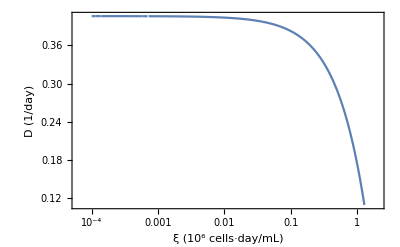

```mathematica
LogLinearPlot[DSteadyState[ξ/0.04629629629629629,0.00001]24,{ξ,0.0001,28.06439 * 0.04629629629629629},
PlotRange->Full,
Frame->True,
LabelStyle->Directive[GrayLevel[0],12],
FrameStyle->GrayLevel[0],
GridLines->None,
Axes->None,
FrameLabel->{"ξ (10^6 cells·day/mL)","D (1/day)"}
]
```

```mathematica
Module[{grid,βlist,colorList,plot,plotopts,ξunit,ξrange,ξmax},
ξunit=0.04629629629629629;
βlist={0.00001,1.99 100,1.99 1000,1.99×100000};
colorList={GrayLevel[0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5]};
plotopts={PlotRange->Full,Frame->True,LabelStyle->Directive[GrayLevel[0],12],FrameStyle->GrayLevel[0],GridLines->None,Axes->None};
ξmax = {28.064393459247096,125.65505579422289,330.2442072813006,600.};
ξrange={-3,Log[Last[ξmax]ξunit]};

showDvsξplot := 
Show[Table[LogLinearPlot[XSteadyState[ξ/ξunit,βlist⟦i⟧]1.111111,{ξ,0.0001,ξmax⟦i⟧ξunit},
Evaluate@plotopts,
FrameLabel->{"ξ (10^6 cells·day/mL)","D (1/day)"},
PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{ξrange,{0,0.8}}];

(*grid=GraphicsGrid[{
{Show[Table[LogLinearPlot[Deq[βlist⟦i⟧,ξ/ξunit]24,{ξ,0.0001,ξmax[βlist⟦i⟧]ξunit},Evaluate@plotopts,FrameLabel->{"ξ (10^6 cells·day/mL)","D (1/day)"},PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{ξrange,{0,0.8}}],
Show[Table[LogLinearPlot[Xeq[βlist⟦i⟧,ξ/ξunit]1.111111,{ξ,0.0001,ξmax[βlist⟦i⟧]ξunit},Evaluate@plotopts,FrameLabel->{"ξ (10^6 cells·day/mL)","X (10^6 cells/mL)"},PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{ξrange,{0,2.8}}]},
{Show[Table[LogLinearPlot[sgeq[βlist⟦i⟧,ξ/ξunit],{ξ,0.0001,ξmax[βlist⟦i⟧]ξunit},Evaluate@plotopts,FrameLabel->{"ξ (10^6 cells·day/mL)","s_g (mM)"},PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{ξrange,{0,15}}],
Show[Table[LogLinearPlot[sleq[βlist⟦i⟧,ξ/ξunit],{ξ,0.0001,ξmax[βlist⟦i⟧]ξunit},Evaluate@plotopts,FrameLabel->{"ξ (10^6 cells·day/mL)","s_l (mM)"},PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{ξrange,{0,18}}]}},
ImageSize->1000];
plot=Legended[grid,LineLegend[colorList,Table["λ_mβ = "<>ToString@NumberForm[N[β vatpmax[0]y],2],{β,βlist}]]];
plot *)

];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0.4+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

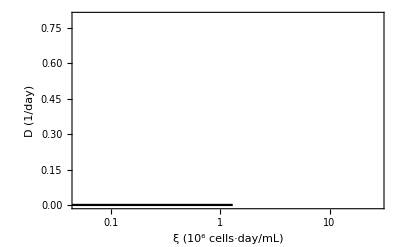

```mathematica
showDvsξplot
```